# 32: Iterative Methods What, Why, and When

Almost all of the algorithms so far have operated on the matrix entries.  These algorithms have typically performed a length m loop loop through all m^2 entries of an m×m square matrix.  They have all required storing a (hopefully small multiple of m^2) entries: our in place algorithms are an attempt to be careful about memory use. They have all required a multiple of m^3 arithmetic operations: our blocked algorithms using the built-in matrix-matrix and matrix-vector operations are an attempt to do this efficiently but there are still a multiple of m^3arithmetic operations.

Almost all large real world matrices inherit some special structure from the physics/engineering they describe.  For instance, almost all standard ways to convert systems of PDEs to linear algebra generate matrices that are almost all zeros: these are the sparse matrices that we have been seen in Mathematica, Julia, etc.

## PDE Discretization 1D: Finite Differences (FD)

Consider the standard PDE
	u_xx=f
on the domain x∈Ω=(0,2) with Dirichlet boundary conditions u|_(∂Ω)=0 on the boundary ∂Ω on the domain Ω.   A standard centered difference approximation is
	u_xx(x)=(u[x-h] - 2 u[x] + u[x+h])/h^2
If we pick n equally spaced internal points
	x_i=0+i h for i=1:n
with h=2/(n+1) then we can approximate the PDE by the set of linear equations
	(u[x_i-h] - 2 u[x_i] + u[x_i+h])/h^2=f[x_i] for i=1:n
This looks a lot cleaner if we write u_i=u[x_i], f_i=f[x_i], and multiply through by h^2. This gives
	u_(i-1)-2 u_i+u_(i+1)=h^2 f_i for i=1:n
Now x_0=0 and x_(n+1)=0 so the Dirichlet boundary conditions say u_0=u_(n+1)=0. This makes the first i=1 and last i=n equations simpler. The first two linear equations are  
	-2 u_1 | + | u_2 | + | 0 u_3 | = | h^2 f_1
u_1 | - | 2 u_2 | + | u_3 | = | h^2 f_2
the generic middle equations are all the same
	u_(i-1)-2 u_i+u_(i+1)=h^2 f_i fori=2:n-1
and the last two equations are 
	u_(n-2) | - | 2 u_(n-1) | + | u_n | = | h^2 f_(n-1)
0 u_(n-2) | + | u_(n-1) | - | 2 u_n | = | h^2 f_n
Writing this as a matrix equation we get
	A.u=f
where A is the n×n symmetric tridiagonal matrix with -2 down the diagonal and 1 down the sub and supper diagonal.   It is not an accident that it is easy to define A and solve the discretized system A.u=f in every computational tool.	

Lets make up a problem that we know the answer to, build the system and look at the  and actually do this.

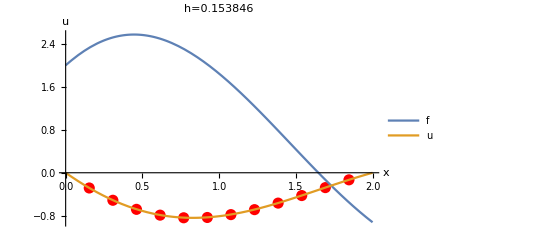

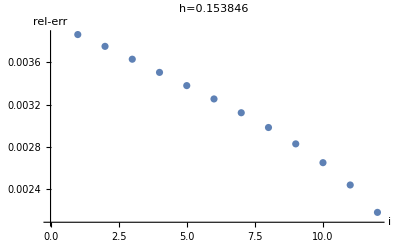

```mathematica
uExact[x_]:= Cos[0.2x+0.1ArcTan[x]](x-2)Sin[x]
f[x_]=D[uExact[x],{x,2}];
n=12;
h=2.0/(n+1);
xs=Table[i h, {i,1,n}];
fs=f[xs];
m=n;
A=SparseArray[{
Band[{1,1}]->-2, 
Band[{1,2}]->1, 
Band[{2,1}]->1},{m,m}];
us=LinearSolve[A,h^2 fs];
Plot[{f[x],uExact[x]},{x,0,2},
AxesLabel->{"x","u"},
PlotLegends->{"f","u"},
PlotLabel->StringForm["h=``",h],
Prolog->{Red,PointSize[0.02],Point[{xs,us}ᵀ]}
]
ListPlot[Abs[(uExact[xs]-us)/uExact[xs]],
AxesLabel->{"i","rel-err"},
PlotLabel->StringForm["h=``",h]]
```

The eigenvalue problem (the minus sign is almost always inserted in this context)
	u_xx=-λ u
on the domain x∈Ω=(0,2) with Dirichlet boundary conditions u|_(∂Ω)=0 on the boundary ∂Ω on the domain Ω produces the same matrix since the discretization of the PDE is just
	(u[x_i-h] - 2 u[x_i] + u[x_i+h])/h^2=-λ u[x_i]
The eigenvectors of this matrix approximate standing waves of a guitar string and the eigenvalues determine the frequencies.

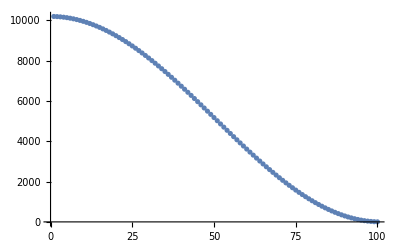

```mathematica
n=100;
h=2.0/(n+1);
m=n;
A=-1/h^2 SparseArray[{
Band[{1,1}]->-2.0, 
Band[{1,2}]->1, 
Band[{2,1}]->1},{n,n}];
{λs,Vs}=Eigensystem[A];
ListPlot[λs]
```

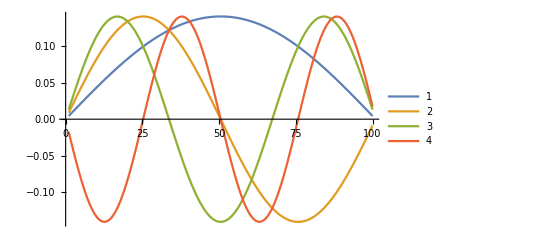

```mathematica
ListPlot[Vs⟦{-1,-2,-3,-4}⟧,
PlotLegends->Automatic,
Joined->True]
```

## PDE Discretization 2D: Finite Differences (FD)

Consider the standard PDE
	u_xx+u_yy=f
on the domain x∈Ω=(0,2)×(0,1) with Dirichlet boundary conditions u|_(∂Ω)=0 on the boundary ∂Ω of the domain Ω.   Standard centered difference approximations are
	u_xx[x,y]=(u[x-h,y] - 2 u[x,y] + u[x+h,y])/h^2 and u_yy[x,y]=(u[x,y-h] - 2 u[x,y] + u[x,y+h])/h^2 
If we want equally spaced internal (x,y) points we can pick
	x_i=0+i h for i=1:1+2n
	y_j=0+j h for j=1:n
with h=1/(n+1) then we can approximate the PDE by the set of linear equations
	(u[x_i-h,y_j] - 2 u[x_i,y_j] + u[x_i+h,y_j])/h^2+(u[x_(i,)y_j-h] - 2 u[x_i,y_j] + u[x_i+h,y_j])/h^2=f[x_i,y_j] for i=1:1+2n and j=1:n
This looks a lot cleaner if we write u_(i,j)=u[x_i,y_j], f_(i,j)=f[x_i,y_j], and multiply through by h^2. This gives
	  |   | u_(i,j+1) |   |   |   |  
u_(i-1,j) | - | 4 u_(i,j) | + | u_(i+1,j) | = | h^2 f_(i,j)
  |   | u_(i,j-1) |   |   |   |  
The differential operator u_xx+u_yy is called the Laplacian.  The pattern above to approximate the Laplacian is called the standard 5 point stencil for the Laplacian.  The Dirichlet boundary conditions 
	u(0,y)=u(2,y)=u(x,0)=u(x,1)=0
simplify the “just-inside” i=j=1 and i=2n, j=n equations like before.  Here is a standard way to convert the block of equations into linear algebra. First number the n(1+2n) interior nodes in some order.  Here is a standard very organized numbering scheme.

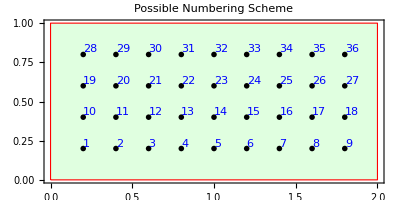

```mathematica
n=4;
h=1/(n+1);
x[i_]:=i*h
y[j_]:=j*h
Graphics[ {
{LightGreen,EdgeForm[Red],Rectangle[{0,0},{2,1}]},
{PointSize[0.01],Table[
{Point[{x[i],y[j]}],Blue, Text[i+(2n+1)(j-1),{x[i],y[j]},{-1,-1}]},
{i,1,1+2n},{j,1, n}]}
},
PlotLabel->"Possible Numbering Scheme",
Frame->True]
```

I am going to make a function that implements this numbering scheme.

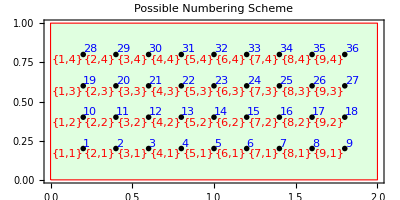

```mathematica
kFromij[{i_,j_},n_]:=i+(2n+1)(j-1);
Graphics[ {
{LightGreen,EdgeForm[Red],Rectangle[{0,0},{2,1}]},
{PointSize[0.01],Table[
{Point[{x[i],y[j]}],
Blue, Text[kFromij[{i,j},n],{x[i],y[j]},{-1,-1}],
Red, Text[{i,j},{x[i],y[j]},{1,1}]},
{i,1,1+2n},{j,1, n}]}
},
PlotLabel->"Possible Numbering Scheme",
Frame->True]
```

```mathematica
ijFromk[k_,n_]:= Module[{i,j},
i=Mod[k,2n+1];
j=1+(k-i)/(2n+1);
{i,j}]
n=12;
{i,j}={5,6};
k=kFromij[{i,j},n]
ijFromk[k,n]
```

130

{5,6}

```mathematica
?Mod
```

```mathematica
xyFromij[{i_,j_},n_]:={i,j}*h
kFromij[{i_,j_},n_]:=i+j*2*n
ijFromk[k_,n_]:=Module[ {i,j},
i=Mod[k,2n]+1;
j=Floor[k/2n]-i+1
] 
h=1.0/(n-1)
```

```mathematica
n=3;
Table[
m=2 n^2;
A=SparseArray[{},{m,m}]
```

Now x_0=0 and x_(n+1)=0 so the Dirichlet boundary conditions say u_0=u_(n+1)=0. This makes the first i=1 and last i=n equations simpler. The first two linear equations are  
	-2 u_1 | + | u_2 | + | 0 u_3 | = | h^2 f_1
u_1 | - | 2 u_2 | + | u_3 | = | h^2 f_2
the generic middle equations are all the same
	u_(i-1)-2 u_i+u_(i+1)=h^2 f_i fori=2:n-1
and the last two equations are 
	u_(n-2) | - | 2 u_(n-1) | + | u_n | = | h^2 f_(n-1)
0 u_(n-2) | + | u_(n-1) | - | 2 u_n | = | h^2 f_n
Writing this as a matrix equation we get
	A.u=f
where A is the n×n symmetric tridiagonal matrix with -2 down the diagonal and 1 down the sub and supper diagonal.   It is not an accident that it is easy to define A and solve the discretized system A.u=f in every computational tool.	

Lets make up a problem that we know the answer to, build the system and look at the  and actually do this.

```mathematica
uExact[x_]:= Cos[0.2x+0.1ArcTan[x]](x-2)Sin[x]
f[x_]=D[uExact[x],{x,2}];
n=12;
h=2.0/(n+1);
xs=Table[i h, {i,1,n}];
fs=f[xs];
m=n;
A=SparseArray[{
Band[{1,1}]->-2, 
Band[{1,2}]->1, 
Band[{2,1}]->1},{m,m}];
us=LinearSolve[A,h^2 fs];
Plot[{f[x],uExact[x]},{x,0,2},
AxesLabel->{"x","u"},
PlotLegends->{"f","u"},
PlotLabel->StringForm["h=``",h],
Prolog->{Red,PointSize[0.02],Point[{xs,us}ᵀ]}
]
ListPlot[Abs[(uExact[xs]-us)/uExact[xs]],
AxesLabel->{"i","rel-err"},
PlotLabel->StringForm["h=``",h]]
```

-Graphics-

-Graphics-

The eigenvalue problem (the minus sign is almost always inserted in this context)
	u_xx=-λ u
on the domain x∈Ω=(0,2) with Dirichlet boundary conditions u|_(∂Ω)=0 on the boundary ∂Ω on the domain Ω produces the same matrix since the discretization of the PDE is just
	(u[x_i-h] - 2 u[x_i] + u[x_i+h])/h^2=-λ u[x_i]
The eigenvectors of this matrix approximate standing waves of a guitar string and the eigenvalues determine the frequencies.

```mathematica
n=100;
h=2.0/(n+1);
m=n;
A=-1/h^2 SparseArray[{
Band[{1,1}]->-2.0, 
Band[{1,2}]->1, 
Band[{2,1}]->1},{n,n}];
{λs,Vs}=Eigensystem[A];
ListPlot[λs]
```

-Graphics-

```mathematica
ListPlot[Vs⟦{-1,-2,-3,-4}⟧,
PlotLegends->Automatic,
Joined->True]
```

-Graphics-